# Analyzing time of flight data

## Prerequisites: sets constants, defines functions

### Constants

```mathematica
μB=9.27400915*10^-28;
kb=1.380658*10^-23;
ℏ=6.62606896*10^-34(2π)^-1;
c=299792458;
a0 = .529*10^-10;
ϵ0 = 8.854*10^-12;
el = 1.602*10^-19;
AMU=1.66*10^-27*kg;
cm=10^-2;mm=10^-3;μm=10^-6;nm = 10^-9;pm=10^-12;fm=10^-15;
kg=1;g=10^-3;ng=10^-9*g;pg=10^-12*g;
Hz=1;kHz=10^3;MHz=10^6;GHz=10^9; THz = 10^12;
Kk=1;mK=10^-3;μK=10^-6;nK=10^-9;
Ww=1;mW=10^-3;μW=10^-6;nW=10^-9;
Pa=1;GPa=10^9;
ms=10^-3;
ohm=1;V=1;mV=10^-3;
ns = 10^-9;
```

```mathematica
mass = 1.44*10^-25;
```

### Functions

```mathematica
convertToXY[set_ ] := (
dims =Dimensions[set];
dataXY=Flatten[Table[{i,j,Mean[set[[i,j]]]},{i,1,dims[[1]]},{j,1,dims[[2]]}],1]
);
```

```mathematica
fitData4[data_,xGuess_,yGuess_,wxGuess_,wyGuess_,ampGuess_]  :=(
dataXY = convertToXY[data];
(*θ=0;*)
fit= 
NonlinearModelFit[dataXY, offset+A*Exp[(-(x-x0)^2)/(2*σx^2)+(-(y-y0)^2)/(2*σy^2)],{{offset,0},{A,ampGuess},{x0,xGuess},{y0,yGuess},{σx,wxGuess},{σy,wyGuess}},{x,y}];
fit["ParameterTable"]
); (*performs 2d fit on the data*)
```

```mathematica
getFlourescence[image_,ROIx1_,ROIx2_,ROIy1_,ROIy2_]:=(
dataToFitTemp = image[[ROIx1;;ROIx2,ROIy1;;ROIy2]];
arrayList = Flatten[Table[Mean[dataToFitTemp[[i,j]]],{i,1,dims[[1]]},{j,1,dims[[2]]}],1];
flourCounts = Total[arrayList];
); (*returns the total number of counts in the data*)
```

```mathematica
fitDataSlices[data_,xBool_]  :=(
dataArray = Table[Mean[data[[i,j]]],{i,1,Dimensions[data][[1]]},{j,1,Dimensions[data][[2]]}];
dataToFit = If[xBool==1, Map[Total, Transpose[dataArray]], Map[Total, dataArray]];
xGuess =Position[dataToFit,Max[Flatten[dataToFit]]];
ampGuess=Max[Flatten[dataToFit]];
fit= 
NonlinearModelFit[dataToFit, offset+A*Exp[(-(x-x0)^2)/(2*σ^2)],{{offset,0},{A,ampGuess},{x0,xGuess[[1,1]]},{σ,30}},x];
Return[{σ/.fit["BestFitParameters"],x0/.fit["BestFitParameters"]}]
);(*performs 1d fit along an axis, the x-axis (y-axis) when xBool = 1 (≠1)*)
```

```mathematica
generateTOFData[images_,ROIx1_,ROIx2_,ROIy1_,ROIy2_]:=(
Clear[σxData,σyData];
dataList = {};
dataListPos = {};
correctCounter = 0;
wGuess = {30,30};
Do[
dataToFitTemp = images[[i]][[ROIx1;;ROIx2,ROIy1;;ROIy2]];
guess =Position[dataToFitTemp,Max[Flatten[dataToFitTemp]]];
ampGuess=Max[Flatten[dataToFitTemp]];
(*Print[guess];
dataToFit = dataToFitTemp[[guess[[1,1]]-25;;guess[[1,1]]+25,guess[[1,2]]-25;;guess[[1,2]]+25]];*)
dataToFit=dataToFitTemp;
fitData4[dataToFit,guess[[1,1]],guess[[1,2]], wGuess[[1]],wGuess[[2]],ampGuess];
If[fit["AdjustedRSquared"]>0.7,
dataPoint = {Abs[σx],Abs[σy]}/. fit["BestFitParameters"];
dataPointPos = {x0,y0}/. fit["BestFitParameters"];
If[Norm[dataPoint]<10000,wGuess=dataPoint];
AppendTo[dataList, {keyVals[[i]],dataPoint}];
AppendTo[dataListPos, {keyVals[[i]],dataPointPos}];
correctCounter=correctCounter+1;
];
Print[fit["AdjustedRSquared"]];,
{i,1,Length[images]}];
σxData =Map[{#[[1]]*10^-3,camScaleFactor*Abs[#[[2,1]]]}&, dataList];
σyData = Map[{#[[1]]*10^-3,camScaleFactor*Abs[#[[2,2]]]}&, dataList];
xPosData =Map[{#[[1]]*10^-3,camScaleFactor*Abs[#[[2,1]]]}&, dataListPos];
yPosData = Map[{#[[1]]*10^-3,camScaleFactor*Abs[#[[2,2]]]}&, dataListPos];
Print["Through out",Length[images]-correctCounter ," fits due to poor t-statistics"];
Return[{σxData,σyData}]
);(*when given a sequences of images, will fit all of the data, and collate it with the present assignemnt of keuy values. Take s awhile since it does 2D fits.*)
```

```mathematica
generateFlourData[images_,ROIx1_,ROIx2_,ROIy1_,ROIy2_]:=(
Clear[σxData,σyData];
dataList = {};
Do[
dataToFitTemp = images[[i]][[ROIx1;;ROIx2,ROIy1;;ROIy2]];
arrayList = Flatten[Table[Mean[dataToFitTemp[[i,j]]],{i,ROIx1,ROIx2},{j,ROIy1,ROIy2}],1];
flourCounts = Total[arrayList];
AppendTo[dataList, {keyVals[[i]],flourCounts}]
,{i,1,Length[images]}];
Return[dataList]
);(*when given a sequences of images, will extract total counts from all of the data, and collate it with the present assignemnt of keuy values.*)
```

```mathematica
fitTOFData[σxData_,σyData_]:=Module[{},
fitx = NonlinearModelFit[σxData, (√(σ0x^2+(σvx*t)^2)),  {{σ0x,.0005},{σvx,.1}}, t];
fity = NonlinearModelFit[σyData, √(σ0y^2+(σvy*t)^2), {{σ0y,.002},σvy}, t];
Return[{fitx,fity}]
];(*returns fit objects on TOF data (= spatial extent versus time, all in SI)*)
```

## Set file location

```mathematica
SetDirectory["/Volumes/kaufman_heap-1/heap/180306/MOT_load/"]
files = Drop[FileNames[],0];
images = Map[ImageData[Import[#,"bmp"]]&, files];
```

/Volumes/kaufman_heap-1/heap/180306/MOT_load

## Extract load time, peak flourescence

```mathematica
a
```

a

```mathematica
initVal = 1;
finVal =2000;
```

```mathematica
numShots = Length[images];
keyFunc[index_]=initVal+(index-1)*(finVal-initVal)/numShots
rawKeys= ToExpression[ Map[StringSplit[StringSplit[#,"."][[1]],"_"][[2]]&,files]];
keyVals =Map[keyFunc,rawKeys];
```

1+1999/20 (-1+index)

```mathematica
initData = Sort[Transpose[{keyVals, images}]];
```

```mathematica
(*Map[ArrayPlot[#[[2]], FrameTicks-> True, FrameLabel-> {"x","y"}]&,initData]*)
```

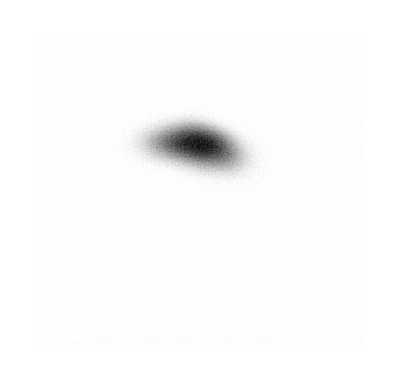

```mathematica
ArrayPlot[images[[3]]]
```

```mathematica
imageDims = Dimensions[images[[1]]];
```

```mathematica
loadData = generateFlourData[images,1,imageDims[[1]],1,imageDims[[2]]];
```

```mathematica
nlm=NonlinearModelFit[loadData, offset+A*(1-Exp[-t/τ]),{{τ,.3},A,offset},t];
```

```mathematica
timeCons = τ/.nlm["BestFitParameters"];
counts = A/.nlm["BestFitParameters"];
```

## Display data

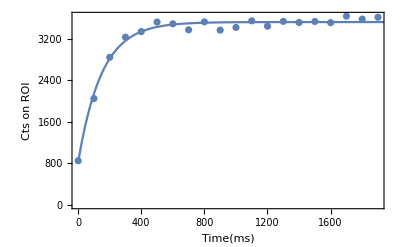

The time constant is 148.854 ms

The counts above background are 2720.34

```mathematica
Show[{ListPlot[dataList, PlotRange-> {0,Max[Transpose[dataList][[2]]]}],Plot[nlm[x], {x,0,2000},PlotRange-> {0,Max[Transpose[dataList][[2]]]}]}, Frame-> True, Axes-> False, FrameLabel-> {"Time(ms)","Cts on ROI"}]
Print["The time constant is ", timeCons, " ms" ]
Print["The counts above background are ", counts ]
```